```mathematica
ClearAll["Global*`"]
```

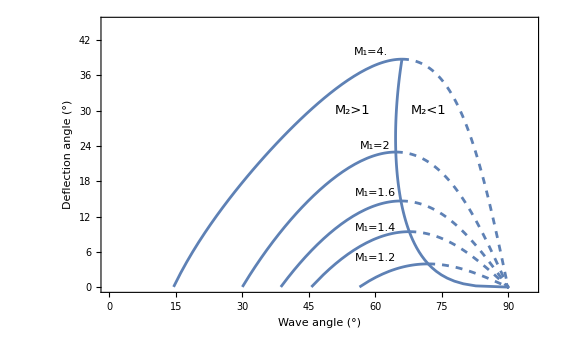

```mathematica
(*Problem 1*)
ClearAll[a,b,c,d,e]
γ=1.4;
δ[M1_]:=ArcTan[(2*Cot[σ*Degree]*(M1^2(Sin[σ*Degree])^2-1))/(M1^2(γ+Cos[2*σ*Degree])+2)]*180/π;
ms={1.2,1.4,1.6,2,4};
maxs=Table[FindMaximum[{δ[m],60<σ<80},{σ,65}],{m,{1.2,1.4,1.6,2,4}}];
maxPoints=Table[{σ/.maxs[[n]][[2]],maxs[[n]][[1]]},{n,Range[5]}];
plots1=Table[Plot[δ[ms[[n]]],{σ,0,maxPoints[[n]][[1]]},PlotRange->{{0,95},{0,45}},Frame->True,FrameLabel->{Style["Wave angle (°)",Italic,FontSize->14],Style["Deflection angle (°)",Italic,FontSize->14]},Epilog->{Text["M_1=4.",{59,40}],Text[Style["M_2>1",FontSize->13],{55,30}],Text["M_1=2",{60,24}],Text["M_1=1.6",{60,16}],Text["M_1=1.4",{60,10}],Text["M_1=1.2",{60,5}],Text[Style["M_2<1",FontSize->13],{72,30}]}],{n,Range[5]}];
plots2=Table[Plot[δ[ms[[n]]],{σ,maxPoints[[n]][[1]],90},PlotStyle->Dashed],{n,Range[5]}];
additionalMaxs=Table[FindMaximum[{δ[m],60<=σ<=90},{σ,65}],{m,Range[.2,4,.025]}];
additionalMaxesPoints=Table[{σ/.additionalMaxs[[n]][[2]],additionalMaxs[[n]][[1]]},{n,Range[Length[additionalMaxs]]}];
PrependTo[additionalMaxesPoints,{90,0}];
(*maxPoints=Prepend[maxPoints]*)
(*Fit a curve to the points*)
Show[plots1,plots2,ListLinePlot[additionalMaxesPoints]]
```

```mathematica
(*Prep*)
(*s:=ArcTan[(2*Cot[σ*Degree]*(4^2(Sin[σ*Degree])^2-1))/(4^2(γ+Cos[2*σ*Degree])+2)]*180/π;
max=FindMaximum[s,{σ,60}]
{σ/.max[[2]],max[[1]]}
plots=Table[Plot[δ[m],{σ,0,maxPoints[[5]][[1]]},PlotRange->{0,40}],{m,{1.2,1.4,1.6,2,4}}];
Show[plots,ListLinePlot[maxPoints]]*)
```

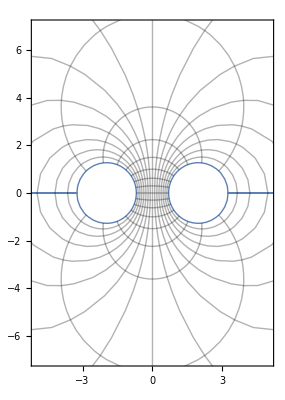

```mathematica
(*Problem 2*)
a=1.5;
x=(a*Sinh[n])/(Cosh[n]-Cos[φ]);
y=(a*Sin[φ])/(Cosh[n]-Cos[φ]);
ParametricPlot[{x,y},{φ,0,2π},{n,-1,1},PlotRange->{{-5,5},{-7,7}},Mesh->15,PlotStyle->None]
```

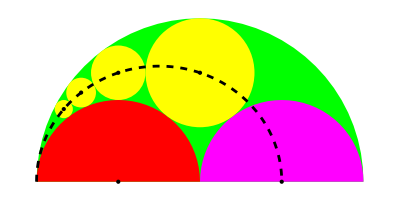

```mathematica
(*Problem 3*)
ClearAll[x,y,n]
R0=0.5;
RL=0.25;
RR=0.25;
d=Table[n^2(1-r)^2+r,{n,Range[4]}];
(*Small circles*)
xn=Table[(r(1+r))/(2*ds),{ds,d}];
yn=Table[(n*r(1-r))/d[[n]],{n,Range[4]}];
rn=Table[(r(1-r))/(2*ds),{ds,d}];
r=RL/(RL+RR);
(*nCircles=Table[]*)
(*ellipse=((4x-(1+r))/(1+r))^2+((2y)/(√r))^2=1*)
semi=Graphics[{Green,Disk[{.5,0},R0,{0,π}],Red,Disk[{0.25,0},RL,{0,π}],Magenta,Disk[{0.75,0},RR,{0,π}],Black,PointSize[Large],Point[{{0.25,0},{0.75,0}}],Yellow,Table[Disk[{xn[[n]],yn[[n]]},rn[[n]]],{n,Range[4]}]}];
nCircCenters=Graphics[{Black,PointSize[Large],Point[Table[{xn[[n]],yn[[n]]},{n,Range[4]}]]}];
Show[semi,nCircCenters,Plot[y/.Solve[((4x-(1+r))/(1+r))^2+((2y)/(√r))^2==1],{x,0,(1+r)/2},PlotRange->{0,0.5},PlotStyle->{Black,Dashed}]]
```

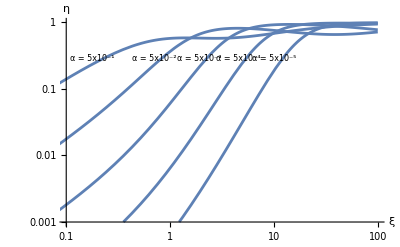

```mathematica
(*Problem 4*)
(*Use Epilog*)
ClearAll[a,n]
n[a_,e_]:=(a*e(3+6*e+4*e^2+2*a*e^3+a^2 e^4))/((1+a*e)(1+a^2*e^4+2*a*e(2+3*e+2 e^2)));
a = {5*10^-1,5*10^-2,5*10^-3,5*10^-4,5*10^-5};
labels={Text[Style["α = 5x10^-1",8],{Log[.18],Log[.29]},Automatic,{1,.5}],Text[Style["α = 5x10^-2",8],{Log[.7],Log[.29]},Automatic,{1,.9}],Text[Style["α = 5x10^-3",8],{Log[1.9],Log[.29]},Automatic,{1,1}],Text[Style["α = 5x10^-4",8],{Log[4.5],Log[.29]},Automatic,{1,1.2}],Text[Style["α = 5x10^-5",8],{Log[10],Log[.29]},Automatic,{1,1.2}]};
plots=Table[LogLogPlot[n[as,es],{es,0.01,100},Epilog->labels,GridLines->Full,PlotRange->{{0.1,100},{0.001,1}},AxesLabel->{Style[ξ,FontSize->14],Style[η,FontSize->14]}],{as,a}];
Show[plots]
```

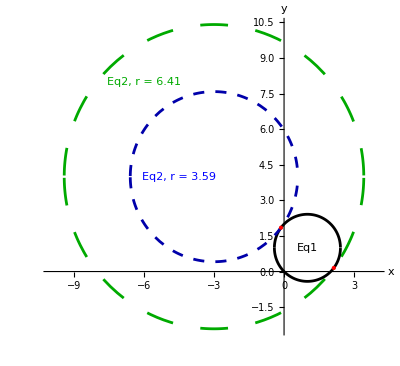

```mathematica
(*Problem 5*)
Eq1=(x-1)^2+(y-1)^2==2;
(*Find radi*)
smallR=√((-3-1)^2+(4-1)^2)-√2;
largeR=√((-3-1)^2+(4-1)^2)+√2;
Eq2=(x+3)^2+(y-4)^2==smallR^2;
Eq3=(x+3)^2+(y-4)^2==largeR^2;
(*Plot Circles*)
orig=Plot[y/.Solve[(x-1)^2+(y-1)^2==2],{x,-1,3},AspectRatio->{1,1},PlotStyle->Black];
small=Plot[y/.Solve[(x+3)^2+(y-4)^2==smallR^2],{x,-8,3},AspectRatio->{1,1},PlotStyle->{Dashing[0.02],Darker[Blue]}];
large=Plot[y/.Solve[(x+3)^2+(y-4)^2==largeR^2],{x,-10,4},AspectRatio->{1,1},PlotStyle->{Dashing[0.05],Darker[Green]}];
(*Get coordinates for intersections*)
smallIntersect=NSolve[{Eq1,Eq2},{x,y}];
largeIntersect=NSolve[{Eq1,Eq3},{x,y}];
(*Plot intersect points*)
smallPt=Graphics[{PointSize[Large],Red,Point[{x/.smallIntersect[[1]][[1]],y/.smallIntersect[[1]][[2]]}]}];
largePt=Graphics[{PointSize[Large],Red,Point[{x/.largeIntersect[[1]][[1]],y/.largeIntersect[[1]][[2]]}]}];
(*Plot labels*)
labels=Graphics[{Darker[Green],Text[Style["Eq2, r = 6.41",Medium],{-6,8}],Blue,Text[Style["Eq2, r = 3.59",Medium],{-4.5,4}],Black,Text[Style["Eq1",Medium],{1,1}]}];
(*Plot everything*)
Show[large,orig,small,smallPt,largePt,labels,AxesLabel->{x,y}]
```